```mathematica
Clear["Global`*"];
```

#### Initialization

```mathematica
(* SET INTERVAL TO 1 BEFORE CHANGING INITIALIZATION PARAMETERS! *)

P           = 20.;                      (* Laser Power [W] *)
nIndex = 1.6;                    (* Refraction index [dimensionless] *)
P           = P  (nIndex^2+1)/(2nIndex);(* Recalculation of Laser Power inside the crystal [W] *)
h           = 31;                       (* Heat Exchange Coefficient [W/m^2/K]*)
k           = 5.2 ;                   (* Thermal Conductivity [W/m/K] *)
c           = 1022;                  (* Thermal Сapacity [J/kg/K] *)
ρ       = 2470;                      (* Density [kg/m^3] *)
lx         = 42. 10^-3;          (* X-size [m] *)
ly         = 5. 10^-3;            (* Y-size [m] *)
lz         = 5. 10^-3;            (* Z-size [m] *)
β           =5.6 10^-3;        (* Volume Absorption Coefficient [1/m] *)
S            = 14. 10^-3;        (* Surface Absorption Coefficient [1/m] *)
t1          = 50.;                    (* Heating Stop Time [s] *)
α            =  k/c/ρ;         (* [m^2/s] *)
H            = h/k;                (* [1/m] *)
A            = P/(k ly lz);(* [K/m] *)

(* HAVE YOU SET THE INTERVAL TO 1? *)

(*
Rest of variables and functions: rootsX [1/m], z [sqrt(m)], u [1/m], γ [1/m^2], P1,P2 and ψ [dimensionless], φ1 and φ2 [m^2]
*)
```

Configuration

```mathematica
numberOfTerms = 6000; 
(*" 
Supposed number of terms in the series calculations.
Min(empiric): 15 000 terms for [interval = 1] Mode.
Good strategy to avoid weird mistakes: gradually increase the number of terms from ~5'000 to 30-40'000 with the step of 10'000.
Be patient: it is pretty long.
Caution: That's not a real number of terms because of duplicates. 
Check the lenght of rootsX to determine the number of terms in the final series calculation. 
"*)
interval = 35;
(*"
Supposed minimal interval between roots of the auxiliary equation (used to speed up the calculation).
Be careful: one lost root can spoil the solution.
Not sure about the value? Use interval = 1, then check the typical interval in the rootsX. Be patient: it is pretty long.
"*)
```

Auxiliary calculations
Auxiliary 1
Trying to find non-zero roots of the auxiliary equation

```mathematica
Off[FindRoot::lstol]
rootsX=Table[x/.FindRoot[Tan[x lx]== (2 H x)/(x^2-H^2), {x, interval  i}],{i,0,numberOfTerms}];
```

```mathematica
rootsX=DeleteDuplicates[Round[rootsX,0.0000001]];
rootsX=Select[Chop[rootsX],#>0&];
```

Auxiliary 2

```mathematica
z = ParallelTable[√(2/(2 H+lx(H^2+rootsX⟦i⟧^2))), {i, 1, Length[rootsX]}];
```

Auxiliary 3

```mathematica
γ = ParallelTable[rootsX⟦i⟧^2 + 2H(1/ly+ 1/lz), {i, 1, Length[rootsX]}];
```

Auxiliary 4

```mathematica
P1 = ParallelTable[Sin[lx * rootsX⟦i⟧]+ H/rootsX⟦i⟧( 1 - Cos[ lx rootsX⟦i⟧] ), {i, 1, Length[rootsX]}];
```

Auxiliary 5

```mathematica
P2 =ParallelTable[1/2(H * Sin[ lx*rootsX⟦i⟧ ] + rootsX⟦i⟧  ( 1 + Cos[ lx*rootsX⟦i⟧] ) ), {i, 1, Length[rootsX]}];
```

Auxiliary 6

```mathematica
u = Function[{e,x}, e Cos[e x] + H Sin[e x]];
```

```mathematica
ψ[g_, t_] = Piecewise[{
{ 1 - Exp[-α* g * t], 0<t< t1 },
{ (Exp[α* g * t1] - 1) Exp[-α* g * t], t>t1 }
}];
```

Basic calculation

```mathematica
φ1[x_, t_] =∑_(i=1)^Length[rootsX] z⟦i⟧^2/γ⟦i⟧  P1⟦i⟧  u[rootsX⟦i⟧, x]  ψ[γ⟦i⟧, t];
φ2[x_, t_] = ∑_(i=1)^Length[rootsX] z⟦i⟧^2/γ⟦i⟧P2⟦i⟧   u[rootsX⟦i⟧, x]  ψ[γ⟦i⟧, t];
T[x_, t_] = A β φ1[x, t] + A S φ2[x, t];
```

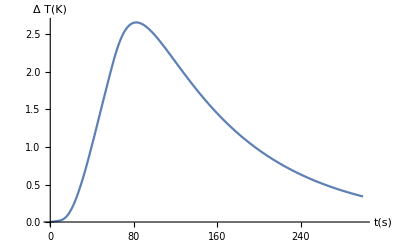

2808 terms were used in the series calculation.

```mathematica
Plot[
T[lx/2, t], 
{t, 0, 300}, 
AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14] 
 ]
Length[rootsX]Text["terms were used in the series calculation." ]
```

Simplification

The core: We consider the temperature distribution of the sample to be almost steady due to continuous laser irradiation, i.e. the end time of exposure is very far from the start time.
Criteria of Simplification: 1/(α γ[[1]]) << t1.

```mathematica
criteria =1/(α γ⟦1⟧);
t1Simple = criteria * 100; (* Hope that x << 100x *)
t1Simple;
```

Recalculation of T(x, t)

```mathematica
ψSimple[g_, t_] = Piecewise[{
{1 - Exp[-α* g * t], 0<t< t1Simple},
{ (Exp[α* g * t1Simple] - 1) Exp[-α* g * t], t>t1Simple }
}];
φ1Simple[x_, t_] = ∑_(i=1)^Length[rootsX] z⟦i⟧^2/γ⟦i⟧ P1⟦i⟧ u[rootsX⟦i⟧, x]  ψSimple[γ⟦i⟧, t];
φ2Simple[x_, t_] = ∑_(i=1)^Length[rootsX] z⟦i⟧^2/γ⟦i⟧ P2⟦i⟧ u[rootsX⟦i⟧, x]  ψSimple[γ⟦i⟧, t];
TSimple[x_, t_] = A β φ1Simple[x, t] + A S φ2Simple[x, t];
```

Plotting

```mathematica
(*Timing[
Plot[{
Legended[TSimple[lx/2, t], Style[ToExpression["T_{Sum}",TeXForm,HoldForm]]],
Legended[A β φ1Simple[lx/2, t], Style[ToExpression["T_{Volume}",TeXForm,HoldForm]]],
Legended[A S φ2Simple[lx/2, t], Style[ToExpression["T_{Surface}",TeXForm,HoldForm]]]},
{t, 0, 20},
AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14],
ImageSize-> Scaled[0.5] ] 
]
Length[rootsX]Text["terms were used in the series calculation." ]*)
```

Plotting in a parallel way

General::munfl: Exp[-719.426] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.752] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-756.308] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{6.37169,Null}

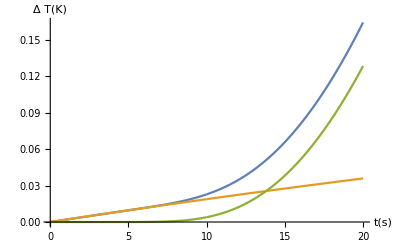

```mathematica
n=2; (* Number of threads to plot *) 
grparallel=With[ {rangeParts=Partition[Range[0,20,20/n],2,1]},ParallelCombine[Function[xrange,
Plot[{ TSimple[lx/2, t], A β φ1Simple[lx/2, t], A S φ2Simple[lx/2, t]}, 
Evaluate[{t,First[xrange],Last[xrange]}],Mesh->None,
MaxRecursion->0]]/@#&,rangeParts,
      Show[{##},PlotRange->All, AxesLabel->{"t(s)", Style[ToExpression["\\Delta T (K)",TeXForm,HoldForm]]},
AxesStyle->Directive[Automatic, 14],
ImageSize-> Scaled[0.5]]&]]; //AbsoluteTiming

grparallel
```

Fitting data

Creating Noisy Data

General::munfl: Exp[-710.704] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-719.964] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.283] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.026] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-712.586] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.152] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-712.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-725.236] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-738.481] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-712.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.262] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-744.533] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-710.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-729.369] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-748.188] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-713.486] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-734.312] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-755.438] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-727.174] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-750.071] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-773.322] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-714.331] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-738.744] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-763.568] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

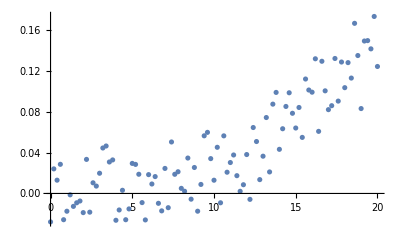

```mathematica
Off[General::munfl]
ProportionalNoiseFactor[x_] := 0.3*x;
ConstantNoiseFactor = 0.04;
SampleData = ParallelTable[
{i, 
TSimple[lx/2, i]+
RandomReal[{-ProportionalNoiseFactor[TSimple[lx/2, i]], ProportionalNoiseFactor[TSimple[lx/2, i]]}] + 
RandomReal[{-ConstantNoiseFactor, ConstantNoiseFactor}]
}, 
{i, 0, 20, 0.2}];
ListPlot[SampleData]
```

Fitting process
2 options available: LinearFit and FindFit (LinearFit works a bit faster, imperceptibly)
Example of import data:  Import[“ExampleData/isomerization.dat”,”Table”,”HeaderLines”→7];

{0.00663979,0.0131217}

{βFit→0.00663979,SFit→0.0131217}

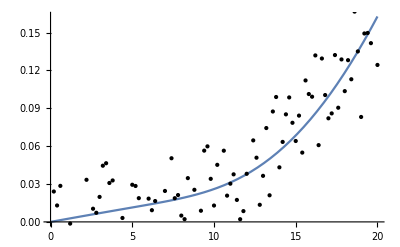

-Graphics-

```mathematica
TSimpleFittingModel= A βFit φ1Simple[lx/2, t] + A SFit φ2Simple[lx/2, t];
linearFit = Fit[SampleData, {A φ1Simple[lx/2, t], A φ2Simple[lx/2, t]}, t, "BestFitParameters"]
fit = FindFit[SampleData, TSimpleFittingModel, {βFit,SFit}, t]
Plot[A linearFit⟦1⟧ φ1Simple[lx/2, t] + A linearFit⟦2⟧ φ2Simple[lx/2, t], {t, 0, 20}, Epilog->Map[Point, SampleData]]
modelf[t_] := Evaluate[TSimpleFittingModel/.fit]
Plot[modelf[t],{t,0,20},Epilog->Map[Point,SampleData]]
```